```mathematica
r=0.0135/2;
R=0.0554/2;
m=0.0145;
M=1.508;
d=0.0667;
mRod=0.00717;
L=2(d+r);
σ=mRod/L;
w=0.0127;
b=R+0.03525/2;
Γ=4/5 m r^2+2 m d^2+mRod/12(L^2+w^2);
```

```mathematica
r1={d Cos[θ],d Sin[θ],0}/.{θ->θ[t]};
r2={-d Cos[θ],-d Sin[θ],0}/.{θ->θ[t]};
```

```mathematica
z={0,0,1};
```

```mathematica
rr1={d,b,0}-r1;
rr2={d,b,0}-r2;
```

```mathematica
F1=(G M m)/(rr1.rr1)(rr1/(√(rr1.rr1)))//FullSimplify
```

{(0.021866 G (0.0667-0.0667 Cos[θ[t]]))/(0.0109521-0.00889778 Cos[θ[t]]-0.00604635 Sin[θ[t]])^(3/2),(0.021866 G (0.045325-0.0667 Sin[θ[t]]))/(0.0109521-0.00889778 Cos[θ[t]]-0.00604635 Sin[θ[t]])^(3/2),0.}

```mathematica
F2=(G M m)/(rr2.rr2)(rr2/(√(rr2.rr2)))//FullSimplify
```

{(0.021866 G (0.0667+0.0667 Cos[θ[t]]))/(0.0109521+0.00889778 Cos[θ[t]]+0.00604635 Sin[θ[t]])^(3/2),(0.021866 G (0.045325+0.0667 Sin[θ[t]]))/(0.0109521+0.00889778 Cos[θ[t]]+0.00604635 Sin[θ[t]])^(3/2),0.}

```mathematica
τSpheres=Cross[r2,F2]+Cross[r1,F1]//FullSimplify
```

{0.,0.,G (Cos[θ[t]] (0.0000661048/(0.0109521-0.00889778 Cos[θ[t]]-0.00604635 Sin[θ[t]])^(3/2)-0.0000661048/(0.0109521+0.00889778 Cos[θ[t]]+0.00604635 Sin[θ[t]])^(3/2))+(-0.0000972794/(0.0109521-0.00889778 Cos[θ[t]]-0.00604635 Sin[θ[t]])^(3/2)+0.0000972794/(0.0109521+0.00889778 Cos[θ[t]]+0.00604635 Sin[θ[t]])^(3/2)) Sin[θ[t]])}

```mathematica
p={l Cos[θ[t]],l Sin[θ[t]],0};
```

```mathematica
rp={d,b,0}-p;
```

```mathematica
torqueRod[l_]=Integrate[Cross[p,(G M σ)/(rp.rp)(rp/(√(rp.rp)))],l,Assumptions->{b>0,d>0,G>0,M>0,σ>0}]//FullSimplify;
```

```mathematica
τRod=torqueRod[L/2]-torqueRod[-L/2]//FullSimplify
```

{0.,0.,(G ((5.43174-4.09191 Cos[θ[t]]-2.7806 Sin[θ[t]])/(√(0.0118981-0.00979823 Cos[θ[t]]-0.00665824 Sin[θ[t]]))+(-5.43174-4.09191 Cos[θ[t]]-2.7806 Sin[θ[t]])/(√(0.0118981+0.00979823 Cos[θ[t]]+0.00665824 Sin[θ[t]]))) (0.00333608 Cos[θ[t]]-0.00490936 Sin[θ[t]]))/(-2.71587+1. Cos[2. θ[t]]+2.52507 Sin[2. θ[t]])}

```mathematica
τTwist=-λ(θ[t]-θ0);
```

Total Torque

```mathematica
τ=2τRod.z+2τSpheres.z+τTwist-β θ'[t];
```

```mathematica
sol=NDSolve[{τ==Γ θ''[t],θ[0]==0.022,θ'[0]==0.0}/.{λ->1.4551 10^-7,β->0.0012,G->1.0 10^-10,θ0->0.0218721},θ[t],{t,0,360}]
```

{{θ[t]→InterpolatingFunction[{{0., 360.}}, <>][t]}}

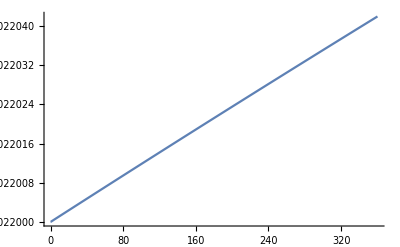

```mathematica
Plot[θ[t]/.sol,{t,0,360}]
```